```mathematica
f[x]
```

f[x]

```mathematica
x^2
```

x^2

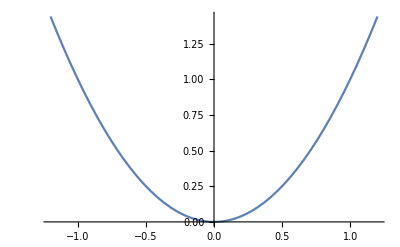

```mathematica
Plot[x^2,{x,-1.2,1.2}]
```

```mathematica
D[x^2,x]
```

2 x

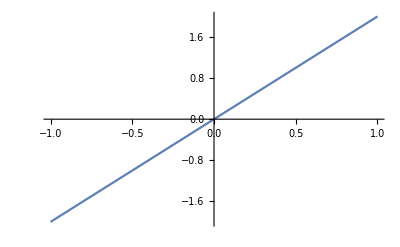

```mathematica
Plot[2 x,{x,-1,1}]
```

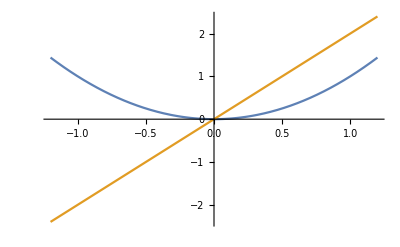

```mathematica
Plot[{x^2,2x},{x,-1.2,1.2}]
```

```mathematica
(1-a)x^2+a 2x
```

2 a x+(1-a) x^2

```mathematica
Manipulate[Plot[2 a x+(1-a) x^2,{x,-8,8}],{a,0,1}]
```

```mathematica
Manipulate[
Plot[
{x^2,2x,2 a x+(1-a) x^2}
,{x,-8,8}],
{a,0,1}]
```

```mathematica
SurfaceData["Torus"]
```

torus

```mathematica
Entity["Surface","Torus"]["ParametricEquations"]
```

Function[{a,c},Function[{u,v},{(c+a Cos[v]) Cos[u],(c+a Cos[v]) Sin[u],a Sin[v]}]]

```mathematica
Function[{a,c},Function[{u,v},{(c+a Cos[v]) Cos[u],(c+a Cos[v]) Sin[u],a Sin[v]}]][1/2,1]
```

Function[{u$,v$},{(1+Cos[v$]/2) Cos[u$],(1+Cos[v$]/2) Sin[u$],Sin[v$]/2}]

```mathematica
Plot3D[Function[{u$,v$},{(1+Cos[v$]/2) Cos[u$],(1+Cos[v$]/2) Sin[u$],Sin[v$]/2}][x,y],{x,-4.004302682640512,4.00428933334778},{y,-0.5408035808098403,0.540803545142123}]
```

-Graphics3D-

```mathematica
{(1+Cos[v$]/2) Cos[u$],(1+Cos[v$]/2) Sin[u$],Sin[v$]/2}/.{v$->θ,u$->ϕ}
```

{(1+Cos[θ]/2) Cos[ϕ],(1+Cos[θ]/2) Sin[ϕ],Sin[θ]/2}

```mathematica
ParametricPlot3D[{(1+Cos[θ]/2) Cos[ϕ],(1+Cos[θ]/2) Sin[ϕ],Sin[θ]/2},{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
1
```

1

```mathematica
f'[x]==x
```

f'[x]==x

```mathematica
DSolve[f'[x]==x,{f[x]},{x}]
```

{{f[x]→x^2/2+C[1]}}

```mathematica
Sin[x]
```

Sin[x]

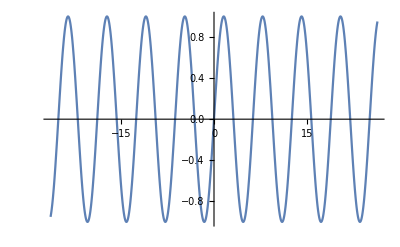

```mathematica
Plot[Sin[x],{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
Sin[x]^2
```

Sin[x]^2

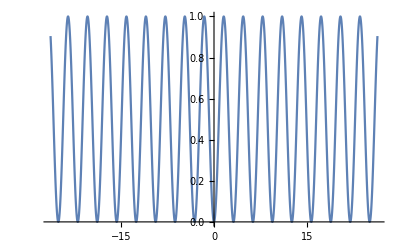

```mathematica
Plot[Sin[x]^2,{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
Quantity[8761,"Seconds"]
```

8761 s

```mathematica
UnitConvert[Quantity[8761,"Seconds"],MixedUnit[{"Hours","Minutes","Seconds"}]]
```

2 26

```mathematica
ListPlot@
Table[
{n,Nest[Sin,x,n]}
,{n,1,100,.1}]
```

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[Sin,x,1.].

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[Sin,x,1.1].

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[Sin,x,1.2].

General::stop: Further output of Nest::intnm will be suppressed during this calculation.

-Graphics-

```mathematica
ListPlot@
Table[
{n,Nest[Sin,x,n]}
,{n,1,100,.1}]
```

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[Sin,x,1.].

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[Sin,x,1.1].

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[Sin,x,1.2].

General::stop: Further output of Nest::intnm will be suppressed during this calculation.

-Graphics-

```mathematica
Table[
{n,Nest[Sin,x,n]}
,{n,1,100,1}]
```

{{1,Sin[x]},98,{100,Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[1]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]}}
 |  |  |  |

```mathematica
ListPlot@
Table[
{n,Nest[Sin,x,n]}
,{n,1,100,1}]
```

-Graphics-

```mathematica
ListPlot@
Table[
{n,Nest[Sin,x,n][n]}
,{n,1,100,1}]
```

-Graphics-

```mathematica
Plot[
Table[
Nest[Sin,x,n]
,{n,1,100,1}]
,{x,-10,10}]
```

$Aborted

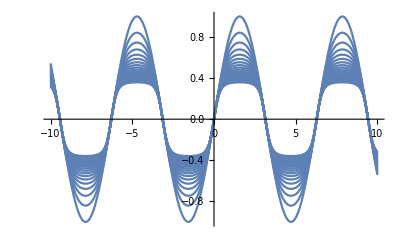

```mathematica
Plot[
Table[
Nest[Sin,x,n]
,{n,1,20,1}]
,{x,-10,10}]
```

```mathematica
Plot[
Table[
Nest[Sin,x,n]
,{n,1,50,1}]
,{x,-10,10}]
```

$Aborted

```mathematica
<<VariationalMethods`
```

```mathematica
VariationalD[y[x] √(1+y'[x]^2),y[x],x]
```

(1+y'[x]^2-y[x] y''[x])/((1+y'[x]^2)^(3/2))

```mathematica
VariationalMethods`VariationalD[y[x] √(1+y'[x]^2),y[x],x]
```

(1+y'[x]^2-y[x] y''[x])/((1+y'[x]^2)^(3/2))

```mathematica
VariationalMethods`VariationalD[ √(1+y'[x]^2),y[x],x]
```

-y''[x]/((1+y'[x]^2)^(3/2))

```mathematica
VariationalMethods`VariationalD[ (√(1+y'[x]^2))/y[x],y[x],x]
```

(-1-y'[x]^2-y[x] y''[x])/(y[x]^2 (1+y'[x]^2)^(3/2))

```mathematica
VariationalMethods`VariationalD[ Normalize[{1,y'[x]}],y[x],x]
```

VariationalD::args: VariationalD takes a single integrand, a function or list of functions, and a list of variables as input.

VariationalD[{1/(√(1+Abs[y'[x]]^2)),y'[x]/(√(1+Abs[y'[x]]^2))},y[x],{x}]

```mathematica
Normalize[{1,y'[x]}]
```

{1/(√(1+Abs[y'[x]]^2)),y'[x]/(√(1+Abs[y'[x]]^2))}

```mathematica
VariationalMethods`VariationalD[ y'[x]/(√(1+y'[x]^2)),y[x],x]
```

(3 y'[x] y''[x])/((1+y'[x]^2)^(5/2))

```mathematica
VariationalMethods`VariationalD[ Normalize[{x-1,y[x]-1}].Normalize[{1,y'[x]}],y[x],x]
```

(-(-1+x) Abs[-1+y[x]] (1+Abs[y'[x]]^2)^2 Abs'[-1+y[x]]+(Abs[-1+x]^2+Abs[-1+y[x]]^2) Abs[y'[x]] (1+Abs[y'[x]]^2) Abs'[y'[x]]-Abs[-1+y[x]] (1+Abs[y'[x]]^2)^2 (-1+y[x]) Abs'[-1+y[x]] y'[x]+(Abs[-1+x]^2+Abs[-1+y[x]]^2) Abs[y'[x]] (1+Abs[y'[x]]^2) Abs'[y'[x]] y'[x]^2+(1+Abs[y'[x]]^2)^2 (-1+y[x]) (Abs[-1+x] Abs'[-1+x]+Abs[-1+y[x]] Abs'[-1+y[x]] y'[x])-(-1+x) Abs[y'[x]] (1+Abs[y'[x]]^2) Abs'[y'[x]] (Abs[-1+x] Abs'[-1+x]+Abs[-1+y[x]] Abs'[-1+y[x]] y'[x])-Abs[y'[x]] (1+Abs[y'[x]]^2) (-1+y[x]) Abs'[y'[x]] y'[x] (Abs[-1+x] Abs'[-1+x]+Abs[-1+y[x]] Abs'[-1+y[x]] y'[x])+2 (Abs[-1+x]^2+Abs[-1+y[x]]^2) Abs[y'[x]] (1+Abs[y'[x]]^2) (-1+y[x]) Abs'[y'[x]] y''[x]-3 (-1+x) (Abs[-1+x]^2+Abs[-1+y[x]]^2) Abs[y'[x]]^2 Abs'[y'[x]]^2 y''[x]+(-1+x) (Abs[-1+x]^2+Abs[-1+y[x]]^2) (1+Abs[y'[x]]^2) Abs'[y'[x]]^2 y''[x]-3 (Abs[-1+x]^2+Abs[-1+y[x]]^2) Abs[y'[x]]^2 (-1+y[x]) Abs'[y'[x]]^2 y'[x] y''[x]+(Abs[-1+x]^2+Abs[-1+y[x]]^2) (1+Abs[y'[x]]^2) (-1+y[x]) Abs'[y'[x]]^2 y'[x] y''[x]+(-1+x) (Abs[-1+x]^2+Abs[-1+y[x]]^2) Abs[y'[x]] (1+Abs[y'[x]]^2) Abs''[y'[x]] y''[x]+(Abs[-1+x]^2+Abs[-1+y[x]]^2) Abs[y'[x]] (1+Abs[y'[x]]^2) (-1+y[x]) y'[x] Abs''[y'[x]] y''[x])/((Abs[-1+x]^2+Abs[-1+y[x]]^2)^(3/2) (1+Abs[y'[x]]^2)^(5/2))

```mathematica
FullSimplify[Normalize[{x-1,y[x]-1}].Normalize[{1,y'[x]}],{x,y[x],y'[x]}∈Reals]
```

(-1+x+(-1+y[x]) y'[x])/(√(((-1+x)^2+(-1+y[x])^2) (1+y'[x]^2)))

```mathematica
VariationalMethods`VariationalD[ (-1+x+(-1+y[x]) y'[x])/(√(((-1+x)^2+(-1+y[x])^2) (1+y'[x]^2))),y[x],x]
```

((2-2 x+x^2-2 y[x]+y[x]^2) y'[x]^3-2 (-1+x) (-1+y[x]) y'[x]^4+(-1+x)^2 y'[x]^5+(-1+x) (2-2 x+x^2-2 y[x]+y[x]^2) y''[x]-2 (-1+x) y'[x]^2 (-1+y[x] (1-2 y''[x])+(2-2 x+x^2) y''[x]+y[x]^2 y''[x])+(-1+y[x]) y'[x] (-1+y[x] (1-6 y''[x])+3 (2-2 x+x^2) y''[x]+3 y[x]^2 y''[x]))/((1+y'[x]^2) ((2-2 x+x^2-2 y[x]+y[x]^2) (1+y'[x]^2))^(3/2))

```mathematica
TraditionalForm[Out[45]]
```

((x-1) (x^2+(y(x))^2-2 y(x)-2 x+2) y''(x)+(x^2+(y(x))^2-2 y(x)-2 x+2) (y'(x))^3-2 (x-1) (y'(x))^2 ((x^2-2 x+2) y''(x)+(y(x))^2 y''(x)+y(x) (1-2 y''(x))-1)+(y(x)-1) y'(x) (3 (x^2-2 x+2) y''(x)+3 (y(x))^2 y''(x)+y(x) (1-6 y''(x))-1)+(x-1)^2 (y'(x))^5-2 (x-1) (y(x)-1) (y'(x))^4)/(((y'(x))^2+1) ((x^2+(y(x))^2-2 y(x)-2 x+2) ((y'(x))^2+1))^(3/2))

```mathematica
Out[45]/.y[x]->x^2
```

((2-2 x-x^2+x^4) y'[x]^3-2 (-1+x) (-1+x^2) y'[x]^4+(-1+x)^2 y'[x]^5+(-1+x) (2-2 x-x^2+x^4) y''[x]-2 (-1+x) y'[x]^2 (-1+x^2 (1-2 y''[x])+x^4 y''[x]+(2-2 x+x^2) y''[x])+(-1+x^2) y'[x] (-1+x^2 (1-6 y''[x])+3 x^4 y''[x]+3 (2-2 x+x^2) y''[x]))/((1+y'[x]^2) ((2-2 x-x^2+x^4) (1+y'[x]^2))^(3/2))

```mathematica
FullSimplify[%47]
```

((-1+x)^4 (2+x (2+x)) ((1+x-y'[x])^2 y'[x] (1+y'[x]^2)+(-2+x^2+x^3) (1+(3+3 x-2 y'[x]) y'[x]) y''[x]))/(((-1+x)^2 (2+x (2+x)) (1+y'[x]^2))^(5/2))

```mathematica
Out[45]/.{y[x]->x^2,y'[x]->2x}
```

(32 (-1+x)^2 x^5-32 (-1+x) x^4 (-1+x^2)+8 x^3 (2-2 x-x^2+x^4)+(-1+x) (2-2 x-x^2+x^4) y''[x]-8 (-1+x) x^2 (-1+x^2 (1-2 y''[x])+x^4 y''[x]+(2-2 x+x^2) y''[x])+2 x (-1+x^2) (-1+x^2 (1-6 y''[x])+3 x^4 y''[x]+3 (2-2 x+x^2) y''[x]))/((1+4 x^2) ((1+4 x^2) (2-2 x-x^2+x^4))^(3/2))

```mathematica
Out[45]/.{y[x]->x^2,y'[x]->2x,y''[x]->2}
```

(32 (-1+x)^2 x^5-32 (-1+x) x^4 (-1+x^2)+2 (-1+x) (2-2 x-x^2+x^4)+8 x^3 (2-2 x-x^2+x^4)-8 (-1+x) x^2 (-1-3 x^2+2 x^4+2 (2-2 x+x^2))+2 x (-1+x^2) (-1-11 x^2+6 x^4+6 (2-2 x+x^2)))/((1+4 x^2) ((1+4 x^2) (2-2 x-x^2+x^4))^(3/2))

```mathematica
FullSimplify[(32 (-1+x)^2 x^5-32 (-1+x) x^4 (-1+x^2)+2 (-1+x) (2-2 x-x^2+x^4)+8 x^3 (2-2 x-x^2+x^4)-8 (-1+x) x^2 (-1-3 x^2+2 x^4+2 (2-2 x+x^2))+2 x (-1+x^2) (-1-11 x^2+6 x^4+6 (2-2 x+x^2)))/((1+4 x^2) ((1+4 x^2) (2-2 x-x^2+x^4))^(3/2))
,x∈Reals]
```

(2 (2+x (13+2 x (5+(-1+x) x))) Sign[-1+x])/((1+4 x^2)^(5/2) (2+x (2+x))^(3/2))

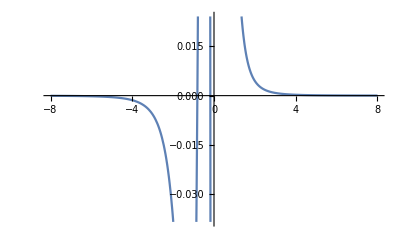

```mathematica
Plot[(2 (2+x (13+2 x (5+(-1+x) x))) Sign[-1+x])/((1+4 x^2)^(5/2) (2+x (2+x))^(3/2)),{x,-8,8}]
```

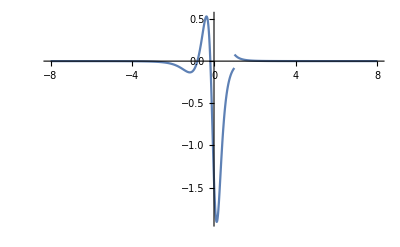

```mathematica
Plot[(2 (2+x (13+2 x (5+(-1+x) x))) Sign[-1+x])/((1+4 x^2)^(5/2) (2+x (2+x))^(3/2)),{x,-8,8},PlotRange->Full]
```

```mathematica
FullSimplify[Out[45],{x,y[x],y'[x]}∈Reals]
```

((1-y[x]+(-1+x) y'[x])^2 (y'[x]+y'[x]^3)-(2+(-2+x) x+(-2+y[x]) y[x]) (1-x+y'[x] (3-3 y[x]+2 (-1+x) y'[x])) y''[x])/((2+(-2+x) x+(-2+y[x]) y[x])^(3/2) (1+y'[x]^2)^(5/2))

```mathematica
FullSimplify[Out[45],{x,y[x],y'[x],y''[x]}∈Reals]
```

((1-y[x]+(-1+x) y'[x])^2 (y'[x]+y'[x]^3)-(2+(-2+x) x+(-2+y[x]) y[x]) (1-x+y'[x] (3-3 y[x]+2 (-1+x) y'[x])) y''[x])/((2+(-2+x) x+(-2+y[x]) y[x])^(3/2) (1+y'[x]^2)^(5/2))

```mathematica
FullSimplify[Out[45],{x,y[x],y'[x],y''[x]}∈Reals]==0
```

((1-y[x]+(-1+x) y'[x])^2 (y'[x]+y'[x]^3)-(2+(-2+x) x+(-2+y[x]) y[x]) (1-x+y'[x] (3-3 y[x]+2 (-1+x) y'[x])) y''[x])/((2+(-2+x) x+(-2+y[x]) y[x])^(3/2) (1+y'[x]^2)^(5/2))==0

```mathematica
DSolve[%56,{y[x],y[x]},{x}]
```

DSolve[((1-y[x]+(-1+x) y'[x])^2 (y'[x]+y'[x]^3)-(2+(-2+x) x+(-2+y[x]) y[x]) (1-x+y'[x] (3-3 y[x]+2 (-1+x) y'[x])) y''[x])/((2+(-2+x) x+(-2+y[x]) y[x])^(3/2) (1+y'[x]^2)^(5/2))==0,{y[x],y[x]},{x}]

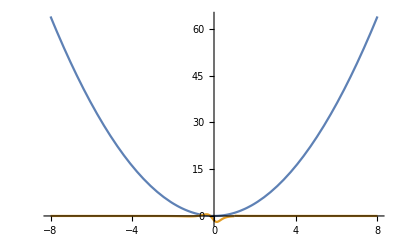

```mathematica
Plot[{x^2,(2 (2+x (13+2 x (5+(-1+x) x))) Sign[-1+x])/((1+4 x^2)^(5/2) (2+x (2+x))^(3/2))},{x,-8,8},PlotRange->Full]
```

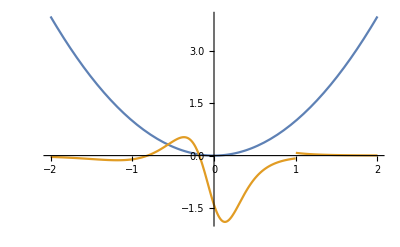

```mathematica
Plot[{x^2,(2 (2+x (13+2 x (5+(-1+x) x))) Sign[-1+x])/((1+4 x^2)^(5/2) (2+x (2+x))^(3/2))},{x,-2,2}]
```

```mathematica
FullSimplify[Normalize[{-x,-y[x]}].Normalize[{1,y'[x]}],{x,y[x],y'[x]}∈Reals]
```

-(x+y[x] y'[x])/(√((x^2+y[x]^2) (1+y'[x]^2)))

```mathematica
-(x+y[x] y'[x])/(√((x^2+y[x]^2) (1+y'[x]^2)))
```

```mathematica
VariationalMethods`VariationalD[ -(x+y[x] y'[x])/(√((x^2+y[x]^2) (1+y'[x]^2))),y[x],x]
```

1/(((x^2+y[x]^2) (1+y'[x]^2))^(5/2))(x^2+y[x]^2) (-3 y[x]^3 y'[x] y''[x]+x y[x] y'[x] (2 y'[x]+2 y'[x]^3-3 x y''[x])-y[x]^2 (y'[x]+y'[x]^3+x y''[x]-2 x y'[x]^2 y''[x])+x^2 (-y'[x]^3-y'[x]^5-x y''[x]+2 x y'[x]^2 y''[x]))

```mathematica
n^2==2
```

n^2==2

```mathematica
n^2==n^2==2
```

n^2==n^2==2

```mathematica
√(n^2)==n^2/n==2
```

√(n^2)==n==2

```mathematica
√(n^2)==n^2/n==2/n
```

√(n^2)==n==2/n

```mathematica
2n==3
```

2 n==3

```mathematica
MultiplySides[2n==3,1/2]
```

n==3/2

```mathematica
2n-n==3-n
```

n==3-n

```mathematica
n==a-n
```

n==a-n

```mathematica
n==α-n
```

n==-n+α

```mathematica
f[x]==2x
```

f[x]==2 x

```mathematica
f[x]==f[x]+f[x]
```

f[x]==2 f[x]

```mathematica
f[x]==2-f[x]
```

f[x]==2-f[x]

```mathematica
Solve[f[x]==2-f[x],f[x]]
```

{{f[x]→1}}

```mathematica
Exp[f[x]^n]
```

ⅇ^(f[x]^n)

```mathematica
Exp[(x^2)^2]
```

ⅇ^(x^4)

```mathematica
Plot[ⅇ^(x^4),{x,-7.896444077714955,7.896444077714955}]
```

-Graphics-

```mathematica
γ==f[α,γ]
```

γ==f[α,γ]

```mathematica
2^x
```

2^x

```mathematica
2^2
```

4

```mathematica
2^4
```

16

```mathematica
f[x]==2f[x]
```

f[x]==2 f[x]

```mathematica
Reduce[f[x]==2 f[x]]
```

f[x]==0

```mathematica
f[x]==2 f[x-1]
```

f[x]==2 f[-1+x]

```mathematica
FindInstance[f[x]==2 f[-1+x],{x}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[f[x]==2 f[-1+x],{x}]

```mathematica
Reduce[f[x]==2 f[-1+x]]
```

f[-1+x]==f[x]/2

```mathematica
2^1.2
```

2.2974

```mathematica
2^(α+β)==2^α 2^β
```

True

```mathematica
2^(1.2+1)
```

4.59479

```mathematica
2^f[x]==Product[2,{n,1,f[x]}]
```

True

```mathematica
f[x]==2^x
```

f[x]==2^x

```mathematica
f[x]==2^f[x-1]
```

f[x]==2^f[-1+x]

```mathematica
f[x]==2f[x-1]
```

f[x]==2 f[-1+x]

```mathematica
Reduce[f[x]==2 f[-1+x]]
```

f[-1+x]==f[x]/2

```mathematica
a[n]==2a[n-1]
```

a[n]==2 a[-1+n]

```mathematica
RSolve[a[n]==2a[n-1],a[n],n]
```

{{a[n]→2^(-1+n) C[1]}}

```mathematica
RSolve[a[n]==1/(1+a[n]),a[n],n]
```

{{a[n]→1/2 (-1-√5),a[n]→1/2 (-1+√5)}}

```mathematica
RSolve[a[n]==2a[n],a[n],n]
```

{{a[n]→0}}

```mathematica
RSolve[a[n]==2/a[n],a[n],n]
```

{{a[n]→-√2,a[n]→√2}}

```mathematica
RSolve[a[n]==1/(1+a[n-1]),a[n],n]
```

{{a[n]→((1/2 (1-√5))^n+(1/2 (1+√5))^n C[1])/((1/2 (1-√5))^(1+n)+(2/(1+√5))^(-1-n) C[1])}}

```mathematica
RSolve[a[n]==2/a[n],a[n],n]
```

{{a[n]→-√2,a[n]→√2}}

```mathematica
RSolve[a[n]==2/a[n-1],a[n],n]
```

{{a[n]→((-1)^n 2^(-n/2)+2^(-n/2) C[1])/((-1)^(1+n) 2^(1/2 (-1-n))+2^(1/2 (-1-n)) C[1])}}

```mathematica
((-1)^n (Subscript[b, 1][n])^-n+(Subscript[b, 1][n])^-n C[1])/((-1)^(1+n) (Subscript[b, 1][n])^(-1-n)+(Subscript[b, 1][n])^(-1-n) C[1])
```

((-1)^n b_1[n]^-n+C[1] b_1[n]^-n)/((-1)^(1+n) b_1[n]^(-1-n)+C[1] b_1[n]^(-1-n))

```mathematica
(-1)^n
```

(-1)^n

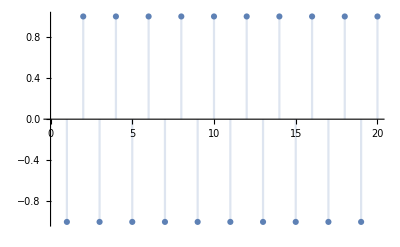

```mathematica
DiscretePlot[(-1)^n,{n,1,20}]
```

```mathematica
(-1)^(n/2)
```

ⅈ^n

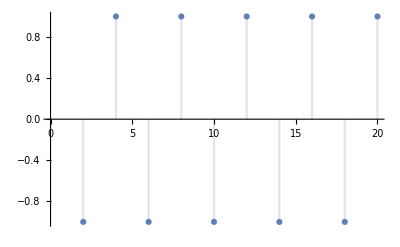

```mathematica
DiscretePlot[ⅈ^n,{n,1,20}]
```

```mathematica
1/(√(1+x^2))
```

1/(√(1+x^2))

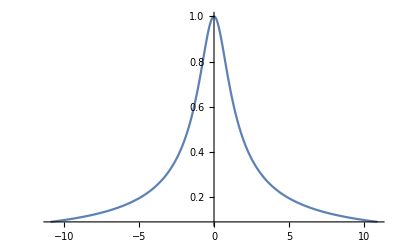

```mathematica
Plot[1/(√(1+x^2)),{x,-10.92,10.92}]
```

```mathematica
Integrate[Integrate[1/(√(1+(x-α)^2))1/(√(1+(x-β)^2)),α],β]
```

ArcSinh[x-α] ArcSinh[x-β]

```mathematica
Manipulate[Plot[ArcSinh[x-α] ArcSinh[x-β],{x,-10.,10.}],{α,-10.,10.},{β,-2,2}]
```

```mathematica
Integrate[ArcSinh[x-α] ArcSinh[x-β],{x,-∞,∞}]
```

∫_(-∞)^∞ ArcSinh[x-α] ArcSinh[x-β]ⅆx

```mathematica
Integrate[Integrate[(x-α)^2(x-β)^2,α],β]
```

1/9 (x-α)^3 (x-β)^3

```mathematica
Integrate[1/9 (x-α)^3 (x-β)^3,{x,-∞,∞}]
```

∫_(-∞)^∞ 1/9 (x-α)^3 (x-β)^3ⅆx

```mathematica
ExpandAll[1/9 (x-α)^3 (x-β)^3]
```

x^6/9-(x^5 α)/3+(x^4 α^2)/3-(x^3 α^3)/9-(x^5 β)/3+x^4 α β-x^3 α^2 β+1/3 x^2 α^3 β+(x^4 β^2)/3-x^3 α β^2+x^2 α^2 β^2-1/3 x α^3 β^2-(x^3 β^3)/9+1/3 x^2 α β^3-1/3 x α^2 β^3+(α^3 β^3)/9

```mathematica
Manipulate[Plot[x^6/9-(x^5 α)/3+(x^4 α^2)/3-(x^3 α^3)/9-(x^5 β)/3+x^4 α β-x^3 α^2 β+1/3 x^2 α^3 β+(x^4 β^2)/3-x^3 α β^2+x^2 α^2 β^2-1/3 x α^3 β^2-(x^3 β^3)/9+1/3 x^2 α β^3-1/3 x α^2 β^3+(α^3 β^3)/9,{x,-8,8}],{α,-8,8},{β,-2,2}]
```

```mathematica
x^6/9
```

x^6/9

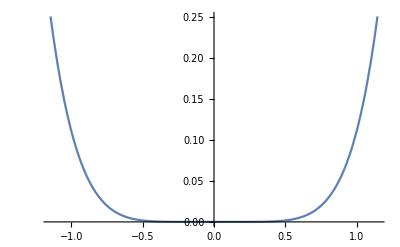

```mathematica
Plot[x^6/9,{x,-1.1449112892755604,1.1449112892755604}]
```

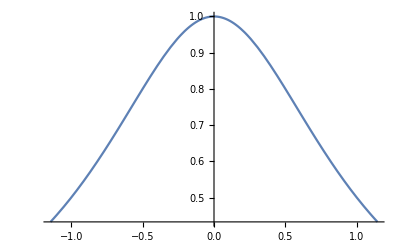

```mathematica
Plot[(1/(√(1+x^2)))^2,{x,-1.1449112892755604,1.1449112892755604}]
```

```mathematica
Normalize@{1,2x}.Normalize@{1,D[(x-1)^2,x]}
```

1/(√(1+4 Abs[-1+x]^2) √(1+4 Abs[x]^2))+(4 (-1+x) x)/(√(1+4 Abs[-1+x]^2) √(1+4 Abs[x]^2))

```mathematica
FullSimplify[Normalize@{1,2x}.Normalize@{1,D[(x-1)^2,x]},x∈Reals]
```

(1-2 x)^2/(√((5+4 (-2+x) x) (1+4 x^2)))

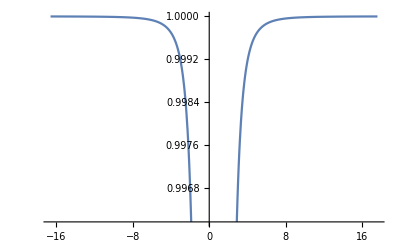

```mathematica
Plot[(1-2 x)^2/(√((5+4 (-2+x) x) (1+4 x^2))),{x,-16.608,17.608}]
```

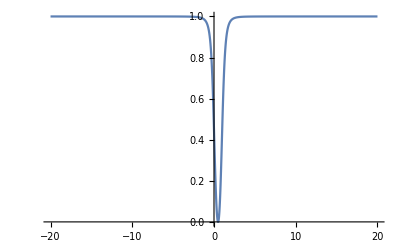

```mathematica
Plot[(1-2 x)^2/(√((5+4 (-2+x) x) (1+4 x^2))),{x,-20,20},PlotRange->Full]
```

```mathematica
FullSimplify[Normalize[D[{x,Sin[x]},x]].Normalize[D[{x,Cos[x]},x]],x∈Reals]
```

(1-Cos[x] Sin[x])/(√((1+Cos[x]^2) (1+Sin[x]^2)))

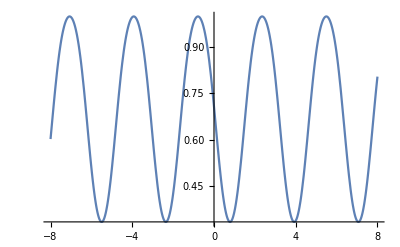

```mathematica
Plot[(1-Cos[x] Sin[x])/(√((1+Cos[x]^2) (1+Sin[x]^2))),{x,-8,8}]
```

```mathematica
ExpandAll[(1+Cos[x]^2) (1+Sin[x]^2)]
```

1+Cos[x]^2+Sin[x]^2+Cos[x]^2 Sin[x]^2

```mathematica
Cos[x]^2+Sin[x]^2==1
```

Cos[x]^2+Sin[x]^2==1

```mathematica
Reduce[Cos[x]^2+Sin[x]^2==1]
```

Cos[x]==-√(1-Sin[x]^2)||Cos[x]==√(1-Sin[x]^2)

```mathematica
1+1+Cos[x]^2 Sin[x]^2
```

2+Cos[x]^2 Sin[x]^2

```mathematica
(1-Cos[x] Sin[x])/(√(2+Cos[x]^2 Sin[x]^2))
```

(1-Cos[x] Sin[x])/(√(2+Cos[x]^2 Sin[x]^2))